```mathematica
Quit[];
```

# PkNW

Alejandro Aviles
avilescervantes@gmail.com


Obtain the non-wiggle linear power spectrum:

call module pknwM[kmin, kmax, Nk, inputPkLinear, hubble] in  file pnw.m 


(Based in the method of  J. Hamann, S. Hannestad, J. Lesgourgues, C. Rampf and Y. Y. Wong, Cosmological
parameters from large scale structure - geometric versus shape information, JCAP 07 (2010)
022, [arxiv:1003.3999].)

```mathematica
SetDirectory[NotebookDirectory[]];

inputpkfile="pk_in.dat";
(*h=0.697;*) 
h=0.6711;(* Hubble *)

outputpknwfile="pkNW_output.dat";
outputpkfile="pk_output.dat";  (*For Plinear output with the same k's as pNW*)

outkmin=0.00001;  
outkmax=10;
outNk=800;

inputpkT=Import[inputpkfile];  
linesInHeader=1;
inputpkT=Drop[inputpkT,linesInHeader];  (* Delete headers *)


<<pnw.m  (*In this .m file you can find the module *)


pknwT=pknwM[outkmin,outkmax,outNk,inputpkT,h];
```

## Plot

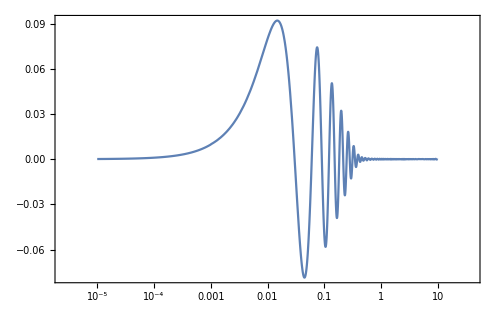

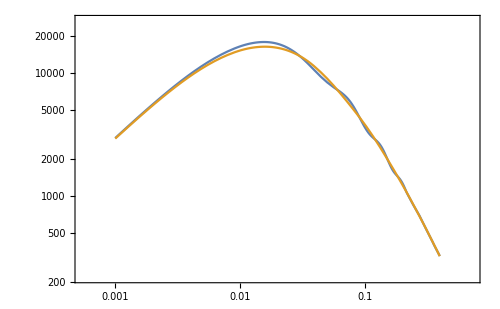

```mathematica
pknw=Interpolation[pknwT];
pk=Interpolation[inputpkT];



prange={outkmin,outkmax};
LogLinearPlot[{(pk[k]-pknw[k])/pknw[k]},{k,prange[[1]],prange[[2]]},Frame->True,ImageSize->500]

LogLogPlot[{pk[k],pknw[k]},{k,0.001,0.4},Frame->True,ImageSize->500]
```

## Export

```mathematica
outkT=Table[outkmin Exp[(i-1)Log[outkmax/outkmin]/(outNk-1)],{i,1,outNk}];
pkT=Table[{outkT[[i]],pk[outkT[[i]]]},{i,1,outNk}];
Length@pkT;
Length@pknwT;
Export[outputpknwfile,pknwT]
Export[outputpkfile,pkT]
```

pkNW_output.dat

pk_output.dat